```mathematica
<<Geometry`
```

## Pythagorean Tiling App - 0.1

### Geometry Explained ( TBD: in development )

#### Starting Point

### Code

```mathematica
pythagoreanTiling[]:=pythagoreanTiling[0.50,Red,Yellow,Blue];
pythagoreanTiling[var_]:=pythagoreanTiling[var,Red,Yellow,Blue];
pythagoreanTiling[var_,cola_,colb_,colc_]:=Module[{
pO,pP,pQ,pR,pS,pT,pU,pV,pW,
dPolyA, dPolyB, dPolyC, dPolyD,
dpoly, dpoly1, dpoly2, dpoly3,
dPolyShadeA, dPolyShadeB
},

pO={0,0};
pP={(1+var)/2,(1-var)/2};
pQ={(1+var+2 var^2)/(2 (1+var)),1/2};
pR={0.50,0.50};
pS={0.50,(1-var)/(1+var) 0.50};
pT={var,1};
pU={0.50 var,0.50};

dPolyA={{{1,{pP,pQ,pR,pS}},{colb,1}},{colb,1,0.005,2 π,2 π}};
dPolyB={{{1,{pQ,pT,pO,pS,pR}},{cola,1}},{cola,1,0.005,2 π,2 π}};
dPolyC={{{1,{pU,pQ}},{RGBColor[0, 0.9500000000000001, 0],1}},{colc,1,0.005,2 π,2 π}};
dPolyD={{{1,{pR, pS}},{RGBColor[0, 0.9500000000000001, 0],1}},{colc,1,0.005,2 π,2 π}};

dpoly={dPolyA,dPolyB,dPolyC,dPolyD};
dpoly1=rot3[dpoly,{-ArcTan[pP[[2]]/pP[[1]]],{0,0}}];
dpoly2=sca3[dpoly1,{{1/√(pP[[2]]^2+pP[[1]]^2),1/√(pP[[2]]^2+pP[[1]]^2)},{0,0}}];
dpoly3={dpoly2,rot3[dpoly2,{π,{0.5,0.5}}]};
Nest[sym4rot,dpoly3,2]
]
```

### App GUI

```mathematica
Manipulate[pythagoreanTiling[a,cola,colb,colc]//toGL//gr,
{{a,.5},0.05,0.95,0.05},{cola,Red},{colb,Yellow},{colc,Blue},ControlPlacement->Right]
```

### App Output

```mathematica
ind:=Tuples[Composition@@{sym4ref,sym4rot},2]
Table[ind[[k]][pythagoreanTiling[0.5,LightBlue,White,Black]]//toGL//gr,{k,1,Length[ind]}]//TableForm
```

-Graphics-

## Pythagorean Tiling App - In Development : Motif on larger Square

### Geometry Explained ( TBD: in development )

#### Starting Point

### Code

```mathematica
pythagoreanTiling[]:=pythagoreanTiling[0.50,Red,Yellow,Blue];
pythagoreanTiling[var_]:=pythagoreanTiling[var,Red,Yellow,Blue];
pythagoreanTiling[var_,cola_,colb_,colc_]:=Module[{
pO,pP,pQ,pR,pS,pT,pU,pV,pW,
dPolyA, dPolyB, dPolyC, dPolyD,dPolyE,
dpoly, dpoly1, dpoly2, dpoly3,
dPolyShadeA, dPolyShadeB
},

pO={0,0};
pP={(1+var)/2,(1-var)/2};
pQ={(1+var+2 var^2)/(2 (1+var)),1/2};
pR={0.50,0.50};
pS={0.50,(1-var)/(1+var) 0.50};
pT={var,1};
pU={0.50 var,0.50};
pV={0.5(-1+var)/(1+var),0.5};
pW={0,0.5};

dPolyA={{{1,{pP,pQ,pR,pS}},{colb,1}},{colb,1,0.005,2 π,2 π}};
dPolyB={{{1,{pQ,pT,pO,pS,pR}},{cola,1}},{cola,1,0.005,2 π,2 π}};
dPolyC={{{1,{pU,pQ}},{RGBColor[0, 0.9500000000000001, 0],1}},{colc,1,0.005,2 π,2 π}};
dPolyD={{{1,{pR, pS}},{RGBColor[0, 0.9500000000000001, 0],1}},{colc,1,0.005,2 π,2 π}};
dPolyE={{{1,{pW, pR}},{RGBColor[0, 0.9500000000000001, 0],1}},{Yellow,1,0.005,2 π,2 π}};

dPolyShadeA={{{1,{pO, pR, pT, pW }},{Gray,1}},{colc,1,0.005,2 π,2 π}};
(*dPolyShadeB={{{1,{pO, pV, pW}},{Gray,1}},{colc,1,0.005,2 π,2 π}};*)

dpoly={dPolyA,dPolyB,dPolyC,dPolyD,dPolyShadeA,dPolyE};
dpoly1=rot3[dpoly,{-ArcTan[pP[[2]]/pP[[1]]],{0,0}}];
dpoly2=sca3[dpoly1,{{1/√(pP[[2]]^2+pP[[1]]^2),1/√(pP[[2]]^2+pP[[1]]^2)},{0,0}}];
dpoly3={dpoly2,rot3[dpoly2,{π,{0.5,0.5}}]};
{dpoly,dpoly1,dpoly2,dpoly3,sym4rot[Nest[sym4rot,dpoly3,1]],dPolyE}
]
```

### App Test

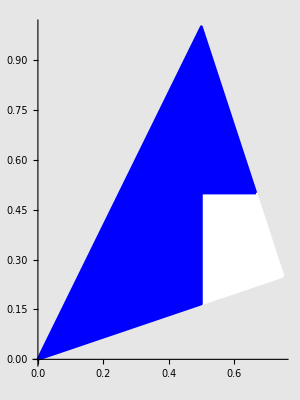

-Graphics-

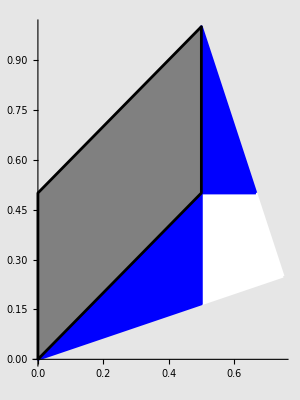

-Graphics-

-Graphics-

```mathematica
pythagoreanTiling[.5,Blue,White,Black][[1]]//toGL//gr2
pythagoreanTiling[.5,LightBlue,White,Black][[5]]//toGL//gr
pythagoreanTiling[.5,LightBlue,White,Black][[6]]//toGL//gr2
```

## DEMO

-Graphics- -Graphics-